The Asymmetric Mach-Zehnder interferometer
Prof. Charlie Ironside
Department of Physics and Astronomy
Curtin University 
Bentley Campus,
Western Australia 6102
email: Charlie.Ironside@curtin.edu.au
web page address:http://oasisapps.curtin.edu.au/staff/profile/view/Charlie.Ironside
Included in the book : “Semiconductor Integrated Optics for Switching Light” by Charlie Ironside 
This note book is based on :-
K. Alhemyari, J. S. Aitchison, C. N. Ironside, G. T. Kennedy, R. S. Grant, and W. Sibbett, “Ultrafast All-Optical Switching in Gaalas Integrated Interferometer in 1.55-Mu-M Spectral Region,” Electronics Letters, vol. 28, pp. 1090-1092, Jun 4 1992.http://dx.doi.org/10.1049/el:19920689



-Graphics-



We are trying to model this result show above

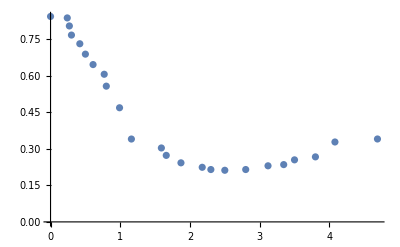

0.005

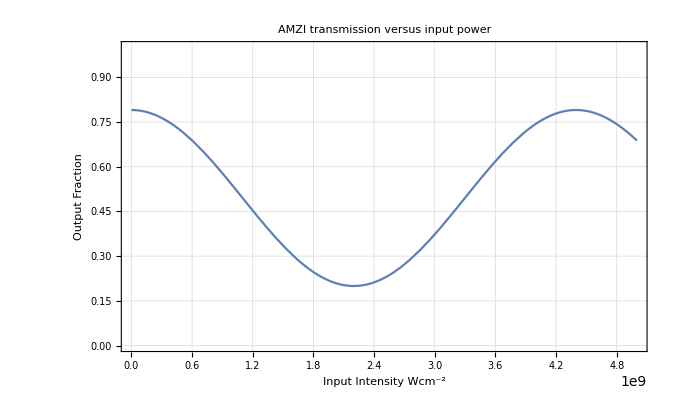

```mathematica
ClearAll[Iin,n2]
Offd:=-0.36
Scale1:=1.5
Data1={{4.69×10^9,Offd +Scale1*0.46721508},{4.08×10^9,Offd +Scale1*0.459},{3.8×10^9,Offd +Scale1*0.4182},{3.5×10^9,Offd +Scale1*0.41004},{3.345×10^9,Offd +Scale1*0.397},{3.12×10^9,Offd +Scale1*0.39372},{2.8×10^9,Offd +Scale1*0.38352},{2.5×10^9,Offd +Scale1*0.38148},{2.3×10^9,Offd +Scale1*0.3835},{2.176×10^9,Offd +Scale1*0.38964},{1.871×10^9,Offd +Scale1*0.40188},{1.66×10^9,Offd +Scale1*0.42228},{1.59×10^9,Offd +Scale1*0.4426},{1.16×10^9,Offd +Scale1*0.4671},{0.99×10^9,Offd +Scale1*0.5528},{0.8×10^9,Offd +Scale1*0.612},{0.77×10^9,Offd +Scale1*0.6446},{0.61×10^9,Offd +Scale1*0.67116},{0.5×10^9,Offd +Scale1*0.69972},{0.42×10^9,Offd +Scale1*0.7282},{0.30×10^9,Offd +Scale1*0.752},{0.27×10^9,Offd +Scale1*0.777},{0.24×10^9,Offd +Scale1*0.799},{0,Offd +Scale1*0.803}};
DataPlot=ListPlot[Data1]
l=0.005 (*Length of AMZI in m *)
Offsetamp=0.2;
ϕ=0;(* offset phase*)
δ= 0.18;(*power split*)
(*Iin= 3.93×10^9(*Input Intensity r Wcm^-2*)*)
λ=1.52×10^-6;(* Wavelength, m *)
n2=5.4×10^-14;(* nonlinear refractive index, cm^2 W^-1*)
Δθ=(2π n2 Iin l(1-2δ))/λ;
T=4δ(1-δ)Cos[Δθ+ϕ]^2+Offsetamp;
Model=Plot[T,{Iin,0,5×10^9},PlotRange->{0,1},Frame->True,PlotLabel->"AMZI transmission versus input power",AxesStyle->Thin,GridLines->Automatic,LabelStyle->{FontFamily->"Times New Roman",24,GrayLevel[0]},FrameLabel->{"Input Intensity Wcm^-2","Output Fraction"},FrameStyle->Thick]
```

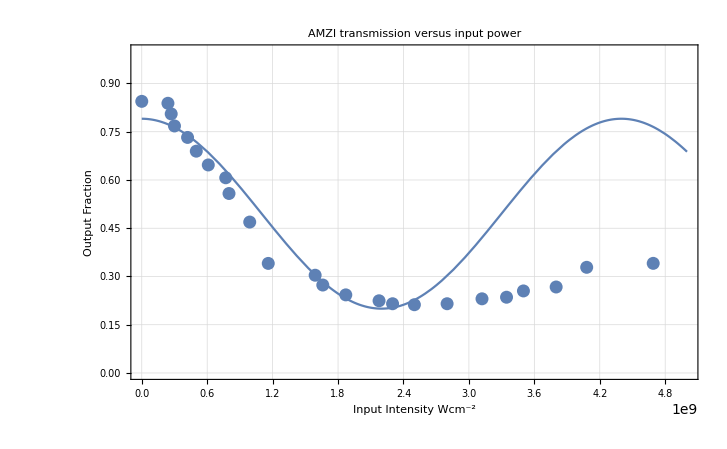

```mathematica
Show[Model,DataPlot]
```